```mathematica
(**)
```

```mathematica
Rho1=3*10^(-7);
C1=1.377*10^6;
k1=82;
Rho2=8.62*10^(-7);
C2=2.1*10^6;
k2=370;
Rho3=7.42*10^(-8);
C3=1.726*10^6;
k3=45;
Rho4=1.18*10^(-9);
C4=1.005*10^6;
k4=28;
a1=k1/(C1*Rho1);
a2=k2/(C2*Rho2);
a3=k3/(C3*Rho3);
a4=k4/(C4*Rho4);
x1=0.6;x2=6;x3=3.6;x4=5;t=1700;
```

```mathematica
Rho1s=300;
C1s=1377;
k1s=0.082;
Rho2s=862;
C2s=2100;
k2s=0.37;
Rho3s=74.2;
C3s=1726;
k3s=0.045;
Rho4s=1.18;
C4s=1005;
k4s=0.028;
ks=8.6;(*Single Layer Model: ks=8.6*)
a1s=k1s/(C1s*Rho1s);
a2s=k2s/(C2s*Rho2s);
a3s=k3s/(C3s*Rho3s);
a4s=k4s/(C4s*Rho4s);
x1s=0.0006;x2s=0.006;x3s=0.0036;x4s=0.005;ts=1700;
```

```mathematica
2*a1s*0.01
```

3.96998×10^-9

```mathematica
0.0001^2(*N1=6*)
```

1.×10^-8

```mathematica
2*a2s*0.01
```

4.08795×10^-9

```mathematica
0.0001^2(*N2=60*)
```

1.×10^-8

```mathematica
2*a3s*0.01
```

7.02745×10^-9

```mathematica
0.0001^2(*N3=36*)
```

1.×10^-8

```mathematica
2*a4s*0.01
```

4.72215×10^-7

```mathematica
0.001^2(*N4=5*)
```

1.×10^-6

```mathematica
1700/0.01*(6+60+36+5)
```

1.819×10^7

```mathematica
Sol=Table[0,{i,1,109},{j,1,170001}];
For[cnt=1,cnt≤170001,cnt++,Sol[[1]][[cnt]]=75;Sol[[109]][[cnt]]=37
]
For[cnt=2,cnt≤109,cnt++,Sol[[cnt]][[1]]=37
]
```

```mathematica
dy=0.01;dx1=0.0001;dx2=0.0001;dx3=0.0001;dx4=0.001;
sigma1=a1s*dy/(dx1*dx1);sigma2=a2s*dy/(dx2*dx2);sigma3=a3s*dy/(dx3*dx3);sigma4=a4s*dy/(dx4*dx4);
```

```mathematica
For[j=2,j≤170001,j++,
{
For[i=2,i≤6,i++,
Sol[[i]][[j]]=sigma1*Sol[[i+1]][[j-1]]+sigma1*Sol[[i-1]][[j-1]]-(2*sigma1-1)*Sol[[i]][[j-1]]
];
For[i=8,i≤66,i++,
Sol[[i]][[j]]=sigma2*Sol[[i+1]][[j-1]]+sigma2*Sol[[i-1]][[j-1]]-(2*sigma2-1)*Sol[[i]][[j-1]]
];
For[i=68,i≤102,i++,
Sol[[i]][[j]]=sigma3*Sol[[i+1]][[j-1]]+sigma3*Sol[[i-1]][[j-1]]-(2*sigma3-1)*Sol[[i]][[j-1]]
];
For[i=104,i≤107,i++,
Sol[[i]][[j]]=sigma4*Sol[[i+1]][[j-1]]+sigma4*Sol[[i-1]][[j-1]]-(2*sigma4-1)*Sol[[i]][[j-1]]
];
Sol[[7]][[j]]=(Sol[[8]][[j]]-Sol[[6]][[j]])/(k1s/dx1+k2s/dx2)*k2s/dx2+Sol[[6]][[j]];
Sol[[67]][[j]]=(Sol[[68]][[j]]-Sol[[66]][[j]])/(k2s/dx2+k3s/dx3)*k3s/dx3+Sol[[66]][[j]];
Sol[[103]][[j]]=(Sol[[104]][[j]]-Sol[[102]][[j]])/(k3s/dx3+k4s/dx4)*k4s/dx4+Sol[[102]][[j]];
Sol[[108]][[j]]=(Sol[[109]][[j]]-Sol[[107]][[j]])/(k4s/dx4+ks)*ks+Sol[[107]][[j]]
}
]
```

```mathematica
mesh=Table[Sol[[i]][[100*j+1]],{i,1,109},{j,0,1700}];
```

```mathematica
solFunc=Table[{x,t,Sol[[x*10+1]][[t*100+1]]},{x,0,10.2},{t,0,1700}];
```

```mathematica
data=Import["D:\\Mod\\temperature.xlsx"];
```

```mathematica
actual=Table[data[[1]][[i]][[2]],{i,3,1703}];
```

```mathematica
mesh[[108]]
```

{37,37.,37.,37.,37.,37.,37.,37.,37.,37.,37.0001,37.0002,37.0005,37.0011,37.002,37.0035,37.0057,37.0087,37.0128,37.018,37.0246,37.0327,37.0423,37.0536,37.0667,37.0816,37.0984,37.117,37.1376,37.16,37.1844,37.2106,37.2387,37.2686,37.3002,37.3335,37.3685,37.4051,37.4432,37.4827,37.5237,37.566,37.6095,37.6543,37.7002,37.7471,37.7951,37.844,37.8937,37.9443,37.9957,38.0477,38.1004,38.1537,38.2075,38.2618,38.3166,38.3718,38.4273,38.4832,38.5393,38.5957,38.6523,38.709,38.766,38.823,38.8801,38.9372,38.9944,39.0516,39.1088,39.166,39.2231,39.2801,39.337,39.3939,39.4506,39.5071,39.5635,39.6197,39.6758,39.7317,39.7873,39.8428,39.898,39.953,40.0078,40.0623,40.1166,40.1706,40.2244,40.2779,40.3311,40.3841,40.4368,40.4891,40.5412,40.5931,40.6446,40.6958,40.7467,40.7974,40.8477,40.8978,40.9475,40.9969,41.0461,41.0949,41.1434,41.1916,41.2396,41.2872,41.3345,41.3815,41.4282,41.4746,41.5207,41.5665,41.612,41.6571,41.702,41.7466,41.7909,41.8349,41.8786,41.9221,41.9652,42.008,42.0506,42.0928,42.1348,42.1765,42.2179,42.259,42.2998,42.3404,42.3806,42.4206,42.4604,42.4998,42.539,42.5779,42.6165,42.6549,42.693,42.7309,42.7684,42.8058,42.8428,42.8796,42.9162,42.9525,42.9885,43.0243,43.0599,43.0952,43.1302,43.165,43.1996,43.2339,43.268,43.3018,43.3354,43.3688,43.4019,43.4348,43.4675,43.5,43.5322,43.5642,43.596,43.6275,43.6588,43.69,43.7208,43.7515,43.782,43.8122,43.8423,43.8721,43.9017,43.9311,43.9603,43.9893,44.0181,44.0467,44.0751,44.1033,44.1313,44.1591,44.1867,44.2141,44.2413,44.2684,44.2952,44.3218,44.3483,44.3746,44.4007,44.4266,44.4523,44.4779,44.5032,44.5284,44.5534,44.5783,44.6029,44.6274,44.6517,44.6759,44.6999,44.7237,44.7473,44.7708,44.7941,44.8173,44.8402,44.8631,44.8857,44.9082,44.9306,44.9528,44.9748,44.9967,45.0184,45.04,45.0614,45.0827,45.1038,45.1248,45.1456,45.1663,45.1868,45.2072,45.2275,45.2476,45.2675,45.2874,45.3071,45.3266,45.346,45.3653,45.3844,45.4034,45.4223,45.441,45.4597,45.4781,45.4965,45.5147,45.5328,45.5507,45.5686,45.5863,45.6039,45.6213,45.6387,45.6559,45.673,45.69,45.7068,45.7236,45.7402,45.7567,45.7731,45.7894,45.8055,45.8216,45.8375,45.8534,45.8691,45.8847,45.9002,45.9155,45.9308,45.946,45.9611,45.976,45.9909,46.0056,46.0203,46.0348,46.0492,46.0636,46.0778,46.0919,46.106,46.1199,46.1338,46.1475,46.1611,46.1747,46.1882,46.2015,46.2148,46.228,46.241,46.254,46.2669,46.2797,46.2925,46.3051,46.3176,46.3301,46.3425,46.3547,46.3669,46.379,46.3911,46.403,46.4148,46.4266,46.4383,46.4499,46.4614,46.4729,46.4842,46.4955,46.5067,46.5178,46.5289,46.5399,46.5508,46.5616,46.5723,46.583,46.5936,46.6041,46.6145,46.6249,46.6352,46.6454,46.6556,46.6656,46.6757,46.6856,46.6955,46.7053,46.715,46.7247,46.7343,46.7438,46.7532,46.7626,46.772,46.7812,46.7904,46.7996,46.8086,46.8176,46.8266,46.8355,46.8443,46.853,46.8617,46.8704,46.8789,46.8874,46.8959,46.9043,46.9126,46.9209,46.9291,46.9373,46.9454,46.9534,46.9614,46.9693,46.9772,46.985,46.9928,47.0005,47.0082,47.0158,47.0233,47.0308,47.0383,47.0457,47.053,47.0603,47.0675,47.0747,47.0819,47.089,47.096,47.103,47.1099,47.1168,47.1237,47.1304,47.1372,47.1439,47.1505,47.1571,47.1637,47.1702,47.1767,47.1831,47.1895,47.1958,47.2021,47.2083,47.2145,47.2207,47.2268,47.2329,47.2389,47.2449,47.2508,47.2567,47.2626,47.2684,47.2742,47.2799,47.2856,47.2913,47.2969,47.3025,47.308,47.3135,47.319,47.3244,47.3298,47.3351,47.3404,47.3457,47.3509,47.3561,47.3613,47.3664,47.3715,47.3766,47.3816,47.3866,47.3915,47.3964,47.4013,47.4062,47.411,47.4158,47.4205,47.4252,47.4299,47.4345,47.4391,47.4437,47.4483,47.4528,47.4573,47.4617,47.4661,47.4705,47.4749,47.4792,47.4835,47.4878,47.492,47.4962,47.5004,47.5045,47.5087,47.5128,47.5168,47.5209,47.5249,47.5288,47.5328,47.5367,47.5406,47.5445,47.5483,47.5521,47.5559,47.5597,47.5634,47.5671,47.5708,47.5744,47.5781,47.5817,47.5852,47.5888,47.5923,47.5958,47.5993,47.6028,47.6062,47.6096,47.613,47.6163,47.6197,47.623,47.6263,47.6295,47.6328,47.636,47.6392,47.6424,47.6455,47.6487,47.6518,47.6548,47.6579,47.661,47.664,47.667,47.67,47.6729,47.6759,47.6788,47.6817,47.6845,47.6874,47.6902,47.6931,47.6958,47.6986,47.7014,47.7041,47.7068,47.7095,47.7122,47.7149,47.7175,47.7201,47.7228,47.7253,47.7279,47.7305,47.733,47.7355,47.738,47.7405,47.743,47.7454,47.7478,47.7502,47.7526,47.755,47.7574,47.7597,47.762,47.7644,47.7667,47.7689,47.7712,47.7734,47.7757,47.7779,47.7801,47.7823,47.7844,47.7866,47.7887,47.7909,47.793,47.7951,47.7971,47.7992,47.8013,47.8033,47.8053,47.8073,47.8093,47.8113,47.8133,47.8152,47.8172,47.8191,47.821,47.8229,47.8248,47.8267,47.8285,47.8304,47.8322,47.834,47.8358,47.8376,47.8394,47.8412,47.8429,47.8447,47.8464,47.8481,47.8498,47.8515,47.8532,47.8549,47.8565,47.8582,47.8598,47.8614,47.8631,47.8647,47.8662,47.8678,47.8694,47.871,47.8725,47.874,47.8756,47.8771,47.8786,47.8801,47.8816,47.883,47.8845,47.8859,47.8874,47.8888,47.8902,47.8917,47.8931,47.8944,47.8958,47.8972,47.8986,47.8999,47.9013,47.9026,47.9039,47.9052,47.9065,47.9078,47.9091,47.9104,47.9117,47.9129,47.9142,47.9154,47.9167,47.9179,47.9191,47.9203,47.9215,47.9227,47.9239,47.9251,47.9262,47.9274,47.9286,47.9297,47.9308,47.932,47.9331,47.9342,47.9353,47.9364,47.9375,47.9386,47.9396,47.9407,47.9418,47.9428,47.9438,47.9449,47.9459,47.9469,47.9479,47.9489,47.9499,47.9509,47.9519,47.9529,47.9539,47.9548,47.9558,47.9568,47.9577,47.9586,47.9596,47.9605,47.9614,47.9623,47.9632,47.9641,47.965,47.9659,47.9668,47.9677,47.9685,47.9694,47.9702,47.9711,47.9719,47.9728,47.9736,47.9744,47.9753,47.9761,47.9769,47.9777,47.9785,47.9793,47.9801,47.9808,47.9816,47.9824,47.9832,47.9839,47.9847,47.9854,47.9862,47.9869,47.9876,47.9884,47.9891,47.9898,47.9905,47.9912,47.9919,47.9926,47.9933,47.994,47.9947,47.9954,47.996,47.9967,47.9974,47.998,47.9987,47.9993,48.,48.0006,48.0013,48.0019,48.0025,48.0031,48.0038,48.0044,48.005,48.0056,48.0062,48.0068,48.0074,48.008,48.0086,48.0091,48.0097,48.0103,48.0109,48.0114,48.012,48.0125,48.0131,48.0136,48.0142,48.0147,48.0153,48.0158,48.0163,48.0169,48.0174,48.0179,48.0184,48.0189,48.0194,48.0199,48.0204,48.0209,48.0214,48.0219,48.0224,48.0229,48.0234,48.0239,48.0243,48.0248,48.0253,48.0257,48.0262,48.0267,48.0271,48.0276,48.028,48.0284,48.0289,48.0293,48.0298,48.0302,48.0306,48.0311,48.0315,48.0319,48.0323,48.0327,48.0331,48.0335,48.034,48.0344,48.0348,48.0352,48.0355,48.0359,48.0363,48.0367,48.0371,48.0375,48.0379,48.0382,48.0386,48.039,48.0393,48.0397,48.0401,48.0404,48.0408,48.0411,48.0415,48.0418,48.0422,48.0425,48.0429,48.0432,48.0436,48.0439,48.0442,48.0446,48.0449,48.0452,48.0455,48.0459,48.0462,48.0465,48.0468,48.0471,48.0474,48.0477,48.048,48.0483,48.0486,48.0489,48.0492,48.0495,48.0498,48.0501,48.0504,48.0507,48.051,48.0513,48.0516,48.0518,48.0521,48.0524,48.0527,48.0529,48.0532,48.0535,48.0537,48.054,48.0543,48.0545,48.0548,48.055,48.0553,48.0555,48.0558,48.056,48.0563,48.0565,48.0568,48.057,48.0573,48.0575,48.0577,48.058,48.0582,48.0584,48.0587,48.0589,48.0591,48.0594,48.0596,48.0598,48.06,48.0602,48.0605,48.0607,48.0609,48.0611,48.0613,48.0615,48.0617,48.0619,48.0622,48.0624,48.0626,48.0628,48.063,48.0632,48.0634,48.0636,48.0638,48.0639,48.0641,48.0643,48.0645,48.0647,48.0649,48.0651,48.0653,48.0654,48.0656,48.0658,48.066,48.0662,48.0663,48.0665,48.0667,48.0669,48.067,48.0672,48.0674,48.0675,48.0677,48.0679,48.068,48.0682,48.0684,48.0685,48.0687,48.0688,48.069,48.0692,48.0693,48.0695,48.0696,48.0698,48.0699,48.0701,48.0702,48.0704,48.0705,48.0707,48.0708,48.071,48.0711,48.0712,48.0714,48.0715,48.0717,48.0718,48.0719,48.0721,48.0722,48.0723,48.0725,48.0726,48.0727,48.0729,48.073,48.0731,48.0733,48.0734,48.0735,48.0736,48.0738,48.0739,48.074,48.0741,48.0742,48.0744,48.0745,48.0746,48.0747,48.0748,48.075,48.0751,48.0752,48.0753,48.0754,48.0755,48.0756,48.0757,48.0759,48.076,48.0761,48.0762,48.0763,48.0764,48.0765,48.0766,48.0767,48.0768,48.0769,48.077,48.0771,48.0772,48.0773,48.0774,48.0775,48.0776,48.0777,48.0778,48.0779,48.078,48.0781,48.0782,48.0783,48.0784,48.0784,48.0785,48.0786,48.0787,48.0788,48.0789,48.079,48.0791,48.0791,48.0792,48.0793,48.0794,48.0795,48.0796,48.0797,48.0797,48.0798,48.0799,48.08,48.0801,48.0801,48.0802,48.0803,48.0804,48.0804,48.0805,48.0806,48.0807,48.0807,48.0808,48.0809,48.081,48.081,48.0811,48.0812,48.0813,48.0813,48.0814,48.0815,48.0815,48.0816,48.0817,48.0817,48.0818,48.0819,48.0819,48.082,48.0821,48.0821,48.0822,48.0823,48.0823,48.0824,48.0825,48.0825,48.0826,48.0826,48.0827,48.0828,48.0828,48.0829,48.0829,48.083,48.0831,48.0831,48.0832,48.0832,48.0833,48.0833,48.0834,48.0835,48.0835,48.0836,48.0836,48.0837,48.0837,48.0838,48.0838,48.0839,48.0839,48.084,48.084,48.0841,48.0841,48.0842,48.0842,48.0843,48.0843,48.0844,48.0844,48.0845,48.0845,48.0846,48.0846,48.0847,48.0847,48.0848,48.0848,48.0849,48.0849,48.085,48.085,48.085,48.0851,48.0851,48.0852,48.0852,48.0853,48.0853,48.0853,48.0854,48.0854,48.0855,48.0855,48.0856,48.0856,48.0856,48.0857,48.0857,48.0858,48.0858,48.0858,48.0859,48.0859,48.0859,48.086,48.086,48.0861,48.0861,48.0861,48.0862,48.0862,48.0862,48.0863,48.0863,48.0863,48.0864,48.0864,48.0865,48.0865,48.0865,48.0866,48.0866,48.0866,48.0867,48.0867,48.0867,48.0868,48.0868,48.0868,48.0868,48.0869,48.0869,48.0869,48.087,48.087,48.087,48.0871,48.0871,48.0871,48.0872,48.0872,48.0872,48.0872,48.0873,48.0873,48.0873,48.0874,48.0874,48.0874,48.0874,48.0875,48.0875,48.0875,48.0875,48.0876,48.0876,48.0876,48.0877,48.0877,48.0877,48.0877,48.0878,48.0878,48.0878,48.0878,48.0879,48.0879,48.0879,48.0879,48.0879,48.088,48.088,48.088,48.088,48.0881,48.0881,48.0881,48.0881,48.0882,48.0882,48.0882,48.0882,48.0882,48.0883,48.0883,48.0883,48.0883,48.0884,48.0884,48.0884,48.0884,48.0884,48.0885,48.0885,48.0885,48.0885,48.0885,48.0886,48.0886,48.0886,48.0886,48.0886,48.0886,48.0887,48.0887,48.0887,48.0887,48.0887,48.0888,48.0888,48.0888,48.0888,48.0888,48.0888,48.0889,48.0889,48.0889,48.0889,48.0889,48.089,48.089,48.089,48.089,48.089,48.089,48.089,48.0891,48.0891,48.0891,48.0891,48.0891,48.0891,48.0892,48.0892,48.0892,48.0892,48.0892,48.0892,48.0892,48.0893,48.0893,48.0893,48.0893,48.0893,48.0893,48.0893,48.0894,48.0894,48.0894,48.0894,48.0894,48.0894,48.0894,48.0895,48.0895,48.0895,48.0895,48.0895,48.0895,48.0895,48.0895,48.0896,48.0896,48.0896,48.0896,48.0896,48.0896,48.0896,48.0896,48.0897,48.0897,48.0897,48.0897,48.0897,48.0897,48.0897,48.0897,48.0897,48.0898,48.0898,48.0898,48.0898,48.0898,48.0898,48.0898,48.0898,48.0898,48.0899,48.0899,48.0899,48.0899,48.0899,48.0899,48.0899,48.0899,48.0899,48.0899,48.09,48.09,48.09,48.09,48.09,48.09,48.09,48.09,48.09,48.09,48.09,48.0901,48.0901,48.0901,48.0901,48.0901,48.0901,48.0901,48.0901,48.0901,48.0901,48.0901,48.0902,48.0902,48.0902,48.0902,48.0902,48.0902,48.0902,48.0902,48.0902,48.0902,48.0902,48.0902,48.0902,48.0903,48.0903,48.0903,48.0903,48.0903,48.0903,48.0903,48.0903,48.0903,48.0903,48.0903,48.0903,48.0903,48.0903,48.0904,48.0904,48.0904,48.0904,48.0904,48.0904,48.0904,48.0904,48.0904,48.0904,48.0904,48.0904,48.0904,48.0904,48.0904,48.0905,48.0905,48.0905,48.0905,48.0905,48.0905,48.0905,48.0905,48.0905,48.0905,48.0905,48.0905,48.0905,48.0905,48.0905,48.0905,48.0905,48.0906,48.0906,48.0906,48.0906,48.0906,48.0906,48.0906,48.0906,48.0906,48.0906,48.0906,48.0906,48.0906,48.0906,48.0906,48.0906,48.0906,48.0906,48.0906,48.0906,48.0907,48.0907,48.0907,48.0907,48.0907,48.0907,48.0907,48.0907,48.0907,48.0907,48.0907,48.0907,48.0907,48.0907,48.0907,48.0907,48.0907,48.0907,48.0907,48.0907,48.0907,48.0907,48.0908,48.0908,48.0908,48.0908,48.0908,48.0908,48.0908,48.0908,48.0908,48.0908,48.0908,48.0908,48.0908,48.0908,48.0908,48.0908,48.0908,48.0908,48.0908,48.0908,48.0908,48.0908,48.0908,48.0908,48.0908,48.0908,48.0908,48.0909,48.0909,48.0909,48.0909,48.0909,48.0909,48.0909,48.0909,48.0909,48.0909,48.0909,48.0909,48.0909,48.0909,48.0909,48.0909,48.0909,48.0909,48.0909,48.0909,48.0909,48.0909,48.0909,48.0909,48.0909,48.0909,48.0909,48.0909,48.0909,48.0909,48.0909,48.0909,48.0909,48.0909,48.091,48.091,48.091,48.091,48.091,48.091,48.091,48.091,48.091,48.091,48.091,48.091,48.091,48.091,48.091,48.091,48.091,48.091,48.091,48.091,48.091,48.091,48.091,48.091,48.091,48.091,48.091,48.091,48.091,48.091,48.091,48.091,48.091,48.091,48.091,48.091,48.091,48.091,48.091,48.091,48.091,48.091,48.091,48.091,48.0911,48.0911,48.0911,48.0911,48.0911,48.0911,48.0911,48.0911,48.0911,48.0911,48.0911,48.0911,48.0911,48.0911,48.0911,48.0911,48.0911,48.0911,48.0911,48.0911,48.0911,48.0911,48.0911,48.0911,48.0911,48.0911,48.0911,48.0911,48.0911,48.0911,48.0911,48.0911,48.0911,48.0911,48.0911,48.0911,48.0911,48.0911,48.0911,48.0911,48.0911,48.0911,48.0911,48.0911,48.0911,48.0911,48.0911,48.0911,48.0911,48.0911,48.0911,48.0911,48.0911,48.0911,48.0911,48.0911,48.0911,48.0911,48.0911,48.0911,48.0911,48.0911,48.0911,48.0912,48.0912,48.0912,48.0912,48.0912,48.0912,48.0912,48.0912,48.0912,48.0912,48.0912,48.0912,48.0912,48.0912,48.0912,48.0912,48.0912,48.0912,48.0912,48.0912,48.0912,48.0912,48.0912,48.0912,48.0912,48.0912,48.0912,48.0912,48.0912,48.0912,48.0912,48.0912,48.0912,48.0912,48.0912,48.0912,48.0912,48.0912,48.0912,48.0912,48.0912,48.0912,48.0912,48.0912,48.0912,48.0912,48.0912,48.0912,48.0912,48.0912,48.0912,48.0912,48.0912,48.0912,48.0912,48.0912,48.0912,48.0912,48.0912,48.0912,48.0912,48.0912,48.0912,48.0912,48.0912,48.0912,48.0912,48.0912,48.0912,48.0912,48.0912,48.0912,48.0912,48.0912,48.0912,48.0912,48.0912,48.0912,48.0912,48.0912,48.0912,48.0912,48.0912,48.0912,48.0912,48.0912,48.0912,48.0912,48.0912,48.0912,48.0912}

```mathematica
actual-mesh[[108]]
```

{0.,0.,0.,0.,-2.45848×10^-12,-7.98224×10^-10,-3.67545×10^-8,-5.61015×10^-7,-4.31785×10^-6,-0.0000211085,-0.000075213,-0.000213097,-0.000508611,-0.00106416,-0.0020079,-0.00348805,0.00433425,0.00129241,-0.00277882,-0.0080376,-0.0046305,-0.0126894,-0.0123293,-0.0236474,-0.026723,-0.0316173,-0.0383747,-0.0470237,-0.0575779,-0.070038,-0.0843923,-0.0906189,-0.108687,-0.118557,-0.140183,-0.153515,-0.168497,-0.185068,-0.203168,-0.222731,-0.243692,-0.255984,-0.279541,-0.294295,-0.320181,-0.337132,-0.355085,-0.383976,-0.403744,-0.424327,-0.445669,-0.467713,-0.490403,-0.503688,-0.527516,-0.551839,-0.57661,-0.591785,-0.61732,-0.633176,-0.659312,-0.685693,-0.702282,-0.719046,-0.745954,-0.762976,-0.790082,-0.807246,-0.824442,-0.851647,-0.868837,-0.885991,-0.903088,-0.930111,-0.947041,-0.963861,-0.980556,-1.00711,-1.02351,-1.03975,-1.0558,-1.08167,-1.09733,-1.11279,-1.12802,-1.14303,-1.1678,-1.18233,-1.19661,-1.21064,-1.2344,-1.2479,-1.26113,-1.27408,-1.29675,-1.30914,-1.32125,-1.33306,-1.35458,-1.36582,-1.37675,-1.39739,-1.40773,-1.41776,-1.4275,-1.44693,-1.45607,-1.47489,-1.48342,-1.49164,-1.50955,-1.51716,-1.53447,-1.54147,-1.55817,-1.56457,-1.57067,-1.58646,-1.59195,-1.60715,-1.61204,-1.62664,-1.64094,-1.64494,-1.65865,-1.66206,-1.67519,-1.68802,-1.69056,-1.70281,-1.70478,-1.71646,-1.72786,-1.73898,-1.73981,-1.75036,-1.76064,-1.76064,-1.77036,-1.77981,-1.78899,-1.7979,-1.79654,-1.80492,-1.81302,-1.82087,-1.82845,-1.83577,-1.84283,-1.84964,-1.84619,-1.85248,-1.85853,-1.86432,-1.86986,-1.87516,-1.88021,-1.88501,-1.88957,-1.89389,-1.89798,-1.90182,-1.91543,-1.9188,-1.92194,-1.92485,-1.92752,-1.92997,-1.9322,-1.93419,-1.94597,-1.94752,-1.94885,-1.94996,-1.95085,-1.96153,-1.96199,-1.96224,-1.96227,-1.9721,-1.97171,-1.97112,-1.98033,-1.97932,-1.97812,-1.98671,-1.9851,-1.9833,-1.99129,-1.98909,-1.9967,-1.99411,-1.99133,-1.99836,-1.99519,-2.00184,-1.99831,-2.00458,-2.00068,-2.00659,-2.00231,-2.00786,-2.00323,-2.00842,-2.01343,-2.00827,-2.01294,-2.00743,-2.01174,-2.00589,-2.00987,-2.01368,-2.00732,-2.0108,-2.01411,-2.00726,-2.01025,-2.01307,-2.01574,-2.00824,-2.01059,-2.01278,-2.00482,-2.0067,-2.00842,-2.01,-2.01142,-2.00269,-2.00382,-2.00479,-2.00562,-2.0063,-1.99684,-1.99723,-1.99748,-1.99758,-1.99755,-1.99737,-1.99706,-1.99661,-1.99602,-1.99529,-1.98443,-1.98344,-1.98231,-1.98105,-1.97965,-1.97813,-1.97648,-1.9747,-1.97279,-1.97075,-1.96859,-1.9663,-1.96388,-1.96135,-1.96869,-1.96591,-1.96301,-1.95999,-1.95685,-1.95359,-1.95021,-1.94672,-1.94311,-1.93939,-1.94555,-1.94159,-1.93753,-1.93335,-1.92907,-1.92467,-1.93016,-1.92555,-1.92082,-1.91599,-1.91105,-1.91601,-1.91086,-1.90561,-1.90025,-1.90479,-1.89923,-1.89357,-1.8978,-1.89194,-1.88598,-1.87992,-1.88376,-1.8775,-1.87115,-1.8747,-1.86816,-1.86152,-1.86479,-1.85796,-1.86104,-1.85404,-1.84693,-1.84974,-1.84246,-1.84509,-1.83763,-1.83009,-1.83245,-1.82473,-1.82692,-1.81903,-1.82105,-1.81299,-1.80484,-1.80661,-1.7983,-1.79991,-1.79143,-1.79287,-1.78424,-1.78552,-1.77672,-1.77785,-1.7789,-1.76987,-1.77076,-1.76157,-1.76231,-1.75298,-1.75357,-1.74409,-1.74453,-1.7449,-1.73519,-1.73541,-1.72557,-1.72565,-1.72566,-1.71559,-1.71546,-1.71526,-1.705,-1.70466,-1.70425,-1.69378,-1.69324,-1.69264,-1.68197,-1.68123,-1.68043,-1.66956,-1.66863,-1.66764,-1.65658,-1.65546,-1.65428,-1.65303,-1.64172,-1.64036,-1.63893,-1.63744,-1.62589,-1.62429,-1.62262,-1.6209,-1.61911,-1.60727,-1.60538,-1.60342,-1.60141,-1.58934,-1.58722,-1.58504,-1.58281,-1.58052,-1.57818,-1.56579,-1.56334,-1.56084,-1.55828,-1.55567,-1.55302,-1.55031,-1.53754,-1.53473,-1.53187,-1.52896,-1.52599,-1.52298,-1.51992,-1.51681,-1.51365,-1.51045,-1.49719,-1.49389,-1.49054,-1.48715,-1.48371,-1.48022,-1.47669,-1.47311,-1.46949,-1.46582,-1.46211,-1.45835,-1.45455,-1.4507,-1.44682,-1.44289,-1.43891,-1.4349,-1.43084,-1.42674,-1.4226,-1.41842,-1.4142,-1.40993,-1.40563,-1.40129,-1.3969,-1.39248,-1.38802,-1.38352,-1.37898,-1.3744,-1.36979,-1.36513,-1.37044,-1.36571,-1.36095,-1.35615,-1.35131,-1.34643,-1.34152,-1.33658,-1.3316,-1.32658,-1.32153,-1.32644,-1.32132,-1.31616,-1.31097,-1.30575,-1.30049,-1.2952,-1.29988,-1.29452,-1.28914,-1.28371,-1.27826,-1.27278,-1.26726,-1.27171,-1.26613,-1.26052,-1.25488,-1.24921,-1.2535,-1.24777,-1.24201,-1.23622,-1.2304,-1.23454,-1.22866,-1.22276,-1.21682,-1.21085,-1.21486,-1.20883,-1.20278,-1.1967,-1.1906,-1.19446,-1.1883,-1.18212,-1.1759,-1.17966,-1.17339,-1.1671,-1.16078,-1.16444,-1.15806,-1.15167,-1.15525,-1.1488,-1.14233,-1.13583,-1.13931,-1.13276,-1.12619,-1.1296,-1.12298,-1.11634,-1.10968,-1.11299,-1.10628,-1.09954,-1.10278,-1.096,-1.0892,-1.09237,-1.08553,-1.07866,-1.08176,-1.07485,-1.06791,-1.07096,-1.06398,-1.05698,-1.05996,-1.05292,-1.04585,-1.04877,-1.04167,-1.04454,-1.0374,-1.03024,-1.03305,-1.02585,-1.01862,-1.02138,-1.01412,-1.01684,-1.00954,-1.00222,-1.00488,-0.997522,-1.00015,-0.992753,-0.985341,-0.98791,-0.980462,-0.982995,-0.975511,-0.968009,-0.97049,-0.962953,-0.965399,-0.957828,-0.960239,-0.952634,-0.945012,-0.947373,-0.939718,-0.942046,-0.934358,-0.936653,-0.928933,-0.931196,-0.923444,-0.925676,-0.917892,-0.910092,-0.912278,-0.904447,-0.906602,-0.898741,-0.900866,-0.892975,-0.89507,-0.88715,-0.889215,-0.881266,-0.883303,-0.875325,-0.877333,-0.869327,-0.871307,-0.863273,-0.865225,-0.857163,-0.859088,-0.851,-0.852897,-0.844782,-0.846653,-0.838512,-0.840357,-0.832189,-0.834008,-0.825815,-0.827609,-0.81939,-0.821159,-0.812916,-0.81466,-0.816391,-0.808111,-0.809819,-0.801514,-0.803198,-0.79487,-0.79653,-0.788178,-0.789815,-0.781441,-0.783055,-0.784657,-0.776249,-0.777829,-0.769398,-0.770956,-0.762504,-0.76404,-0.765565,-0.75708,-0.758584,-0.750078,-0.751561,-0.743034,-0.744496,-0.745949,-0.73739,-0.738822,-0.730244,-0.731656,-0.733058,-0.72445,-0.725832,-0.717204,-0.718567,-0.719921,-0.711265,-0.712599,-0.703924,-0.70524,-0.706546,-0.697844,-0.699132,-0.690411,-0.691681,-0.692942,-0.684195,-0.685438,-0.686673,-0.6779,-0.679117,-0.670326,-0.671527,-0.672719,-0.663903,-0.665078,-0.666245,-0.657404,-0.658555,-0.659698,-0.650833,-0.65196,-0.653079,-0.64419,-0.645293,-0.636388,-0.637476,-0.638556,-0.629629,-0.630694,-0.631751,-0.622802,-0.623844,-0.62488,-0.615908,-0.616929,-0.617943,-0.608949,-0.609949,-0.610942,-0.601927,-0.602906,-0.603878,-0.594843,-0.595801,-0.596753,-0.597697,-0.588636,-0.589567,-0.590492,-0.581411,-0.582323,-0.583229,-0.574128,-0.575021,-0.575908,-0.566788,-0.567663,-0.568531,-0.569393,-0.560249,-0.561099,-0.561943,-0.552782,-0.553614,-0.55444,-0.545261,-0.546076,-0.546885,-0.547688,-0.538486,-0.539279,-0.540065,-0.530846,-0.531622,-0.532392,-0.533157,-0.523917,-0.524671,-0.525419,-0.526163,-0.516901,-0.517635,-0.518363,-0.509085,-0.509803,-0.510516,-0.511224,-0.501927,-0.502625,-0.503317,-0.504006,-0.494689,-0.495367,-0.496041,-0.49671,-0.487374,-0.488034,-0.488689,-0.489339,-0.479985,-0.480626,-0.481263,-0.481896,-0.472523,-0.473147,-0.473766,-0.474381,-0.464991,-0.465597,-0.466199,-0.466797,-0.45739,-0.45798,-0.458565,-0.459146,-0.449723,-0.450296,-0.450865,-0.45143,-0.451991,-0.442548,-0.443101,-0.44365,-0.444195,-0.434737,-0.435275,-0.435809,-0.436339,-0.436865,-0.427388,-0.427907,-0.428423,-0.428934,-0.419443,-0.419947,-0.420449,-0.420946,-0.42144,-0.411931,-0.412418,-0.412902,-0.413382,-0.413859,-0.404333,-0.404803,-0.40527,-0.405734,-0.406195,-0.396652,-0.397106,-0.397557,-0.398005,-0.398449,-0.388891,-0.389329,-0.389764,-0.390197,-0.390626,-0.381052,-0.381475,-0.381895,-0.382313,-0.382727,-0.373138,-0.373547,-0.373953,-0.374355,-0.374755,-0.365153,-0.365547,-0.365939,-0.366327,-0.366714,-0.367097,-0.357478,-0.357856,-0.358231,-0.358604,-0.358974,-0.359342,-0.349707,-0.350069,-0.350429,-0.350786,-0.351141,-0.341493,-0.341843,-0.342191,-0.342536,-0.342878,-0.343218,-0.333556,-0.333892,-0.334225,-0.334555,-0.334884,-0.33521,-0.325534,-0.325855,-0.326174,-0.326491,-0.326806,-0.327119,-0.327429,-0.317737,-0.318043,-0.318347,-0.318649,-0.318949,-0.319246,-0.309542,-0.309835,-0.310126,-0.310415,-0.310703,-0.310988,-0.311271,-0.301552,-0.301832,-0.302109,-0.302384,-0.302658,-0.302929,-0.293199,-0.293466,-0.293732,-0.293996,-0.294258,-0.294518,-0.294777,-0.285034,-0.285288,-0.285541,-0.285793,-0.286042,-0.28629,-0.286536,-0.28678,-0.277023,-0.277263,-0.277503,-0.27774,-0.277976,-0.27821,-0.278443,-0.268673,-0.268903,-0.26913,-0.269356,-0.269581,-0.269804,-0.270025,-0.270245,-0.260463,-0.26068,-0.260895,-0.261109,-0.261321,-0.261531,-0.261741,-0.261948,-0.252155,-0.252359,-0.252563,-0.252765,-0.252965,-0.253164,-0.253362,-0.253558,-0.243753,-0.243947,-0.244139,-0.24433,-0.24452,-0.244708,-0.244895,-0.24508,-0.245264,-0.235447,-0.235629,-0.23581,-0.235989,-0.236167,-0.236343,-0.236519,-0.236693,-0.236866,-0.227038,-0.227208,-0.227377,-0.227546,-0.227712,-0.227878,-0.228043,-0.228206,-0.228369,-0.21853,-0.21869,-0.218849,-0.219007,-0.219163,-0.219319,-0.219474,-0.219627,-0.219779,-0.219931,-0.210081,-0.21023,-0.210378,-0.210525,-0.210671,-0.210816,-0.21096,-0.211103,-0.211245,-0.211386,-0.201526,-0.201665,-0.201803,-0.20194,-0.202076,-0.202212,-0.202346,-0.202479,-0.202611,-0.202743,-0.202873,-0.193003,-0.193131,-0.193259,-0.193386,-0.193512,-0.193637,-0.193761,-0.193885,-0.194007,-0.194129,-0.194249,-0.184369,-0.184488,-0.184607,-0.184724,-0.18484,-0.184956,-0.185071,-0.185185,-0.185299,-0.185411,-0.185523,-0.175634,-0.175744,-0.175853,-0.175962,-0.17607,-0.176177,-0.176283,-0.176389,-0.176494,-0.176598,-0.176701,-0.176804,-0.176906,-0.167007,-0.167108,-0.167208,-0.167307,-0.167405,-0.167503,-0.1676,-0.167696,-0.167792,-0.167887,-0.167981,-0.168075,-0.168168,-0.158261,-0.158352,-0.158443,-0.158534,-0.158624,-0.158713,-0.158801,-0.158889,-0.158977,-0.159063,-0.159149,-0.159235,-0.15932,-0.149404,-0.149488,-0.149571,-0.149654,-0.149735,-0.149817,-0.149898,-0.149978,-0.150058,-0.150137,-0.150215,-0.150293,-0.150371,-0.150448,-0.150524,-0.1406,-0.140675,-0.14075,-0.140824,-0.140898,-0.140971,-0.141044,-0.141116,-0.141188,-0.141259,-0.14133,-0.1414,-0.14147,-0.141539,-0.141607,-0.141676,-0.131743,-0.131811,-0.131878,-0.131944,-0.13201,-0.132075,-0.13214,-0.132205,-0.132269,-0.132332,-0.132395,-0.132458,-0.13252,-0.132582,-0.132644,-0.132705,-0.132765,-0.122825,-0.122885,-0.122944,-0.123003,-0.123061,-0.123119,-0.123177,-0.123234,-0.123291,-0.123348,-0.123404,-0.123459,-0.123514,-0.123569,-0.123624,-0.123678,-0.123731,-0.123785,-0.113838,-0.11389,-0.113943,-0.113994,-0.114046,-0.114097,-0.114148,-0.114198,-0.114248,-0.114298,-0.114347,-0.114396,-0.114445,-0.114493,-0.114541,-0.114589,-0.114636,-0.114683,-0.11473,-0.114776,-0.104822,-0.104868,-0.104913,-0.104958,-0.105003,-0.105047,-0.105091,-0.105135,-0.105179,-0.105222,-0.105265,-0.105307,-0.105349,-0.105391,-0.105433,-0.105474,-0.105515,-0.105556,-0.105597,-0.105637,-0.105677,-0.105717,-0.095756,-0.0957951,-0.0958339,-0.0958725,-0.0959108,-0.0959488,-0.0959866,-0.0960241,-0.0960613,-0.0960983,-0.096135,-0.0961714,-0.0962076,-0.0962435,-0.0962792,-0.0963147,-0.0963499,-0.0963848,-0.0964195,-0.0964539,-0.0964881,-0.0965221,-0.0965558,-0.0965893,-0.0866226,-0.0866556,-0.0866884,-0.086721,-0.0867533,-0.0867854,-0.0868173,-0.086849,-0.0868804,-0.0869116,-0.0869426,-0.0869734,-0.087004,-0.0870343,-0.0870644,-0.0870944,-0.0871241,-0.0871536,-0.0871829,-0.087212,-0.0872409,-0.0872695,-0.087298,-0.0873263,-0.0873544,-0.0873823,-0.08741,-0.0774375,-0.0774648,-0.0774919,-0.0775188,-0.0775455,-0.0775721,-0.0775984,-0.0776246,-0.0776506,-0.0776764,-0.077702,-0.0777275,-0.0777528,-0.0777778,-0.0778028,-0.0778275,-0.0778521,-0.0778765,-0.0779007,-0.0779247,-0.0779486,-0.0779723,-0.0779959,-0.0780193,-0.0780425,-0.0780655,-0.0780884,-0.0781112,-0.0781337,-0.0781562,-0.0681784,-0.0682005,-0.0682225,-0.0682443,-0.0682659,-0.0682874,-0.0683087,-0.0683299,-0.068351,-0.0683718,-0.0683926,-0.0684132,-0.0684336,-0.0684539,-0.0684741,-0.0684941,-0.068514,-0.0685338,-0.0685534,-0.0685729,-0.0685922,-0.0686114,-0.0686304,-0.0686494,-0.0686682,-0.0686868,-0.0687054,-0.0687238,-0.068742,-0.0687602,-0.0687782,-0.0687961,-0.0688139,-0.0688315,-0.068849,-0.0588664,-0.0588837,-0.0589008,-0.0589179,-0.0589348,-0.0589516,-0.0589682,-0.0589848,-0.0590012,-0.0590176,-0.0590338,-0.0590499,-0.0590659,-0.0590817,-0.0590975,-0.0591131,-0.0591287,-0.0591441,-0.0591594,-0.0591746,-0.0591897,-0.0592048,-0.0592196,-0.0592344,-0.0592491,-0.0592637,-0.0592782,-0.0592926,-0.0593069,-0.059321,-0.0593351,-0.0593491,-0.059363,-0.0593768,-0.0593905,-0.059404,-0.0594175,-0.0594309,-0.0594443,-0.0594575,-0.0594706,-0.0594836,-0.0494966,-0.0495094,-0.0495222,-0.0495348,-0.0495474,-0.0495599,-0.0495723,-0.0495846,-0.0495968,-0.049609,-0.049621,-0.049633,-0.0496449,-0.0496567,-0.0496684,-0.0496801,-0.0496916,-0.0497031,-0.0497145,-0.0497258,-0.0497371,-0.0497482,-0.0497593,-0.0497703,-0.0497812,-0.0497921,-0.0498029,-0.0498136,-0.0498242,-0.0498347,-0.0498452,-0.0498556,-0.0498659,-0.0498762,-0.0498864,-0.0498965,-0.0499065,-0.0499165,-0.0499264,-0.0499362,-0.049946,-0.0499557,-0.0499653,-0.0499748,-0.0499843,-0.0499938,-0.0500031,-0.0500124,-0.0500216,-0.0500308,-0.0500399,-0.0400489,-0.0400579,-0.0400668,-0.0400756,-0.0400844,-0.0400931,-0.0401018,-0.0401104,-0.0401189,-0.0401274,-0.0401358,-0.0401442,-0.0401525,-0.0401607,-0.0401689,-0.0401771,-0.0401851,-0.0401931,-0.0402011,-0.040209,-0.0402168,-0.0402246,-0.0402324,-0.04024,-0.0402477,-0.0402553,-0.0402628,-0.0402702,-0.0402777,-0.040285,-0.0402923,-0.0402996,-0.0403068,-0.040314,-0.0403211,-0.0403281,-0.0403351,-0.0403421,-0.040349,-0.0403559,-0.0403627,-0.0403695,-0.0403762,-0.0403828,-0.0403895,-0.040396,-0.0404026,-0.0404091,-0.0404155,-0.0404219,-0.0404283,-0.0404346,-0.0404408,-0.040447,-0.0404532,-0.0404593,-0.0404654,-0.0404715,-0.0404775,-0.0404834,-0.0404894,-0.0404952,-0.0405011,-0.0405069,-0.0405126,-0.0305183,-0.030524,-0.0305296,-0.0305352,-0.0305408,-0.0305463,-0.0305518,-0.0305572,-0.0305626,-0.030568,-0.0305733,-0.0305786,-0.0305839,-0.0305891,-0.0305942,-0.0305994,-0.0306045,-0.0306096,-0.0306146,-0.0306196,-0.0306246,-0.0306295,-0.0306344,-0.0306392,-0.0306441,-0.0306489,-0.0306536,-0.0306583,-0.030663,-0.0306677,-0.0306723,-0.0306769,-0.0306815,-0.030686,-0.0306905,-0.030695,-0.0306994,-0.0307038,-0.0307082,-0.0307125,-0.0307168,-0.0307211,-0.0307253,-0.0307296,-0.0307338,-0.0307379,-0.030742,-0.0307461,-0.0307502,-0.0307543,-0.0307583,-0.0307623,-0.0307662,-0.0307702,-0.0307741,-0.030778,-0.0307818,-0.0307856,-0.0307894,-0.0307932,-0.0307969,-0.0308007,-0.0308044,-0.030808,-0.0308117,-0.0308153,-0.0308189,-0.0308224,-0.030826,-0.0308295,-0.030833,-0.0308364,-0.0308399,-0.0308433,-0.0308467,-0.03085,-0.0308534,-0.0308567,-0.03086,-0.0308633,-0.0308665,-0.0308698,-0.030873,-0.0308762,-0.0308793,-0.0308825,-0.0308856,-0.0308887,-0.0308917,-0.0308948,-0.0308978,-0.0309008,-0.0309038,-0.0209068,-0.0209097,-0.0209127,-0.0209156,-0.0209185,-0.0209213,-0.0209242,-0.020927,-0.0209298,-0.0209326,-0.0209353,-0.0209381,-0.0209408,-0.0209435,-0.0209462,-0.0209489,-0.0209515,-0.0209542,-0.0209568,-0.0209594,-0.020962,-0.0209645,-0.0209671,-0.0209696,-0.0209721,-0.0209746,-0.020977,-0.0209795,-0.0209819,-0.0209844,-0.0209868,-0.0209891,-0.0209915,-0.0209939,-0.0209962,-0.0209985,-0.0210008,-0.0210031,-0.0210054,-0.0210076,-0.0210099,-0.0210121,-0.0210143,-0.0210165,-0.0210187,-0.0210208,-0.021023,-0.0210251,-0.0210272,-0.0210293,-0.0210314,-0.0210335,-0.0210355,-0.0210376,-0.0210396,-0.0210416,-0.0210436,-0.0210456,-0.0210476,-0.0210495,-0.0210515,-0.0210534,-0.0210553,-0.0210572,-0.0210591,-0.021061,-0.0210629,-0.0210647,-0.0210666,-0.0210684,-0.0210702,-0.021072,-0.0210738,-0.0210755,-0.0210773,-0.0210791,-0.0210808,-0.0210825,-0.0210842,-0.0210859,-0.0210876,-0.0210893,-0.021091,-0.0210926,-0.0210943,-0.0210959,-0.0210975,-0.0210991,-0.0211007,-0.0211023,-0.0211039,-0.0211054,-0.021107,-0.0211085,-0.0211101,-0.0211116,-0.0211131,-0.0211146,-0.0211161,-0.0211175,-0.021119,-0.0211205,-0.0211219,-0.0211234,-0.0211248,-0.0211262,-0.0211276,-0.021129,-0.0211304,-0.0211318,-0.0211331,-0.0211345,-0.0211358,-0.0211372,-0.0211385,-0.0211398,-0.0211411,-0.0211424,-0.0211437,-0.021145,-0.0211463,-0.0211475,-0.0211488,-0.0211501,-0.0211513,-0.0211525,-0.0211537,-0.021155,-0.0211562,-0.0211574,-0.0211585,-0.0211597,-0.0211609,-0.0211621,-0.0211632,-0.0211644,-0.0211655,-0.0211666,-0.0211677,-0.0211689,-0.02117,-0.0211711,-0.0211722,-0.0211732,-0.0211743,-0.0211754,-0.0211764,-0.0211775,-0.0211785,-0.0211796,-0.0211806,-0.0211816,-0.0211827,-0.0211837,-0.0211847,-0.0211857,-0.0211867,-0.0211876,-0.0111886,-0.0111896,-0.0111905,-0.0111915,-0.0111924,-0.0111934,-0.0111943,-0.0111952,-0.0111962,-0.0111971,-0.011198,-0.0111989,-0.0111998,-0.0112007,-0.0112016,-0.0112024,-0.0112033,-0.0112042,-0.011205,-0.0112059,-0.0112067,-0.0112076,-0.0112084,-0.0112092,-0.0112101,-0.0112109,-0.0112117,-0.0112125,-0.0112133,-0.0112141,-0.0112149,-0.0112157,-0.0112164,-0.0112172,-0.011218,-0.0112187,-0.0112195,-0.0112202,-0.011221,-0.0112217,-0.0112225,-0.0112232,-0.0112239,-0.0112246,-0.0112254,-0.0112261,-0.0112268,-0.0112275,-0.0112282,-0.0112289,-0.0112295,-0.0112302,-0.0112309,-0.0112316,-0.0112322,-0.0112329}

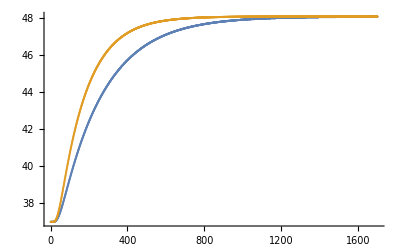

```mathematica
ListPlot[{actual,mesh[[108]]},PlotRange->All]
```

```mathematica
ListPlot3D[mesh]
```

```mathematica
Export["D:\\Mod\\mesh1.xlsx",mesh];
```